# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP
∅ → K
K → ∅ 

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK]+ k[11]k_d-k_d[K],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP] ,
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=100000;

pars={};
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,10];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
(*Export["saturationSampling.csv",transPars];*)
Export["unsaturationSampling.csv",transPars];
```

{16190.,Null}

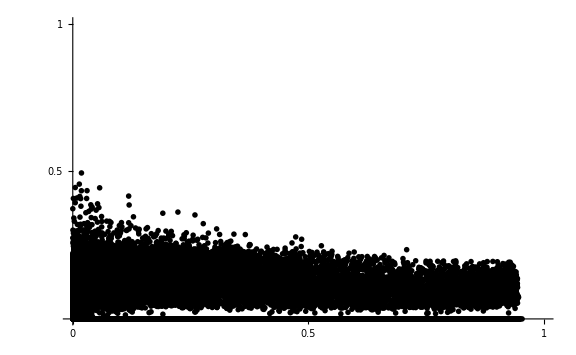

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[15]]]
```

{0.954394,46581}

```mathematica
maxAndIndex[transPars[[16]]]
```

{0.494328,69663}

```mathematica
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
pars[[usIndex]]
```

{0.00824242,0.0142975,0.389576,0.00995311,107.866,0.00631495,2.75791,0.00442517,124.866,0.0176944,0.00634784,0.0001,0.1,0.1,0.954394,0.,47503,48.9994,10838.1,0.00160454,0.000141707}

```mathematica
pars[[adIndex]]
```

{0.735571,118.646,582.997,706.839,0.00242219,59.3703,0.58786,0.00121274,151.948,0.165247,7.60963,0.0001,0.1,0.1,0.0184361,0.494328,71037,953.876,0.0839974,0.00206297,0.00108753}

{a→-0.000757508,b→0.998489,hillK→864.572,n→1.9195}

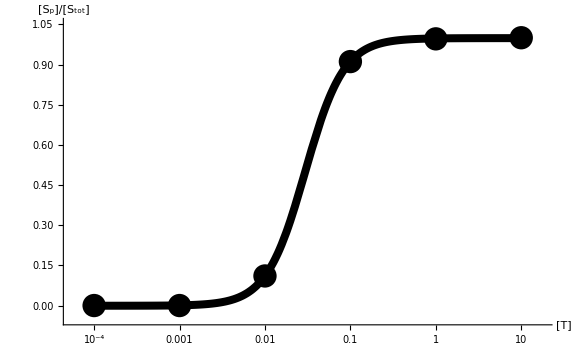

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
stepNum=5;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];totT=pars[[usIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[T]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}], PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

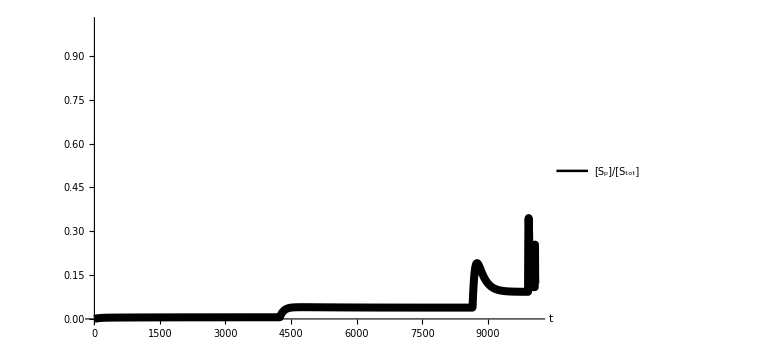

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]];
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

7.60963

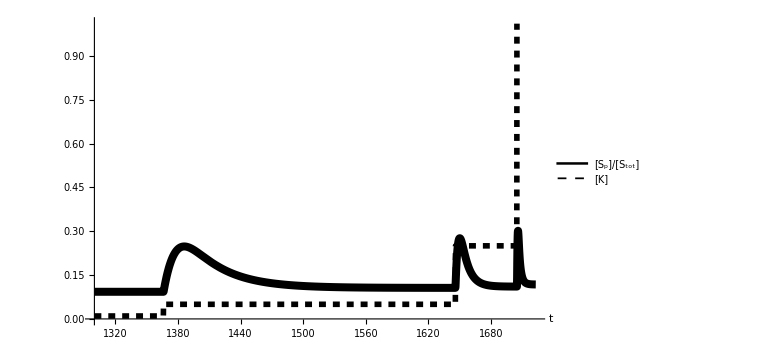

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=3;
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=pars[[adIndex]][[11]]
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,1300,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.25,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,1300,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.55,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

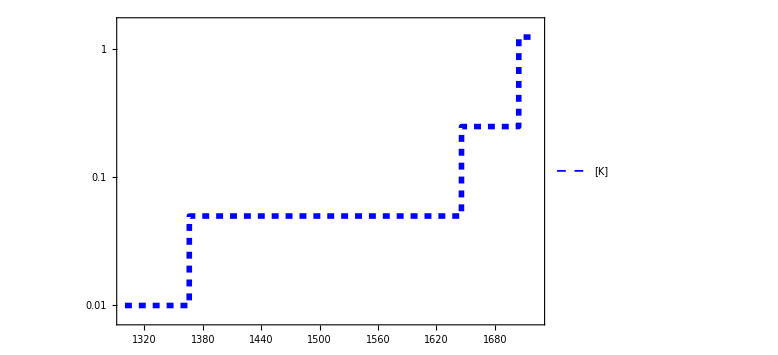

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,1300,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.15,0.9}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

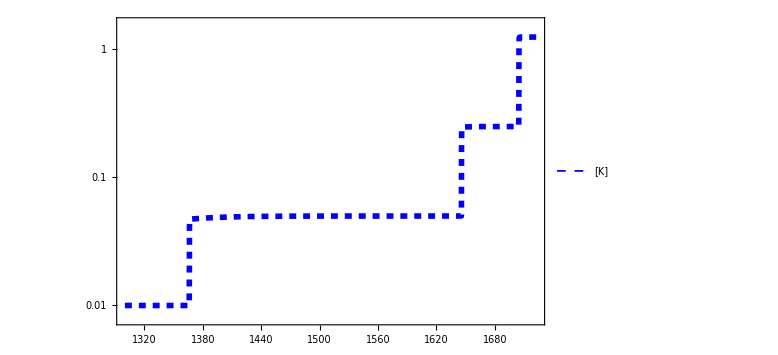

```mathematica
actualInput=LogPlot[{{x[1][t]}/.sol},{t,1300,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.65,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

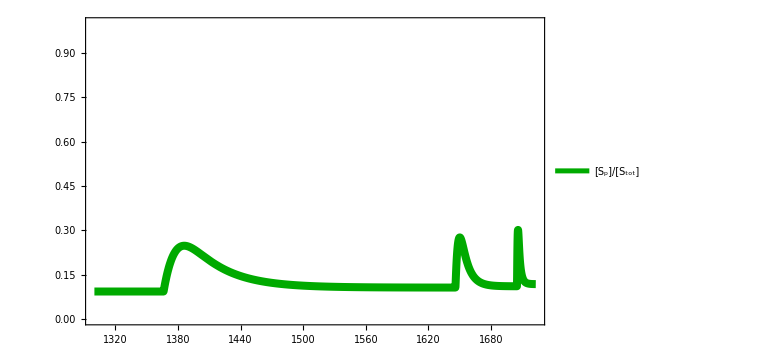

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,1300,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.4,0.9}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{output,input}]
Export["scaffoldTitrationUnsaturatedVaringKAd.eps",adPlot];
Export["scaffoldTitrationUnsaturatedVaringKAd.pdf",adPlot];
```

-Graphics--Graphics-

```mathematica
us10index=Reverse[Ordering[transPars[[15]],-10]]
```

{46581,86053,55163,22701,73649,35579,78074,83646,35959,96101}

```mathematica
ad10index=Reverse[Ordering[transPars[[16]],-10]]
```

{69663,54715,21683,47613,38276,15415,96639,73216,46486,3761}

```mathematica
us10pars=pars[[us10index]]
```

{{0.00824242,0.0142975,0.389576,0.00995311,107.866,0.00631495,2.75791,0.00442517,124.866,0.0176944,0.00634784,0.0001,0.1,0.1,0.954394,0.,47503,48.9994,10838.1,0.00160454,0.000141707},{81.81,779.915,0.0709024,0.0236294,1.48281,0.00181968,0.0051667,465.845,388.389,25.7394,4.51435,0.0001,0.1,0.1,0.950402,0.,87739,9.53411,62.8297,90163.1,0.0662722},{0.00743688,0.0113029,0.671015,0.00492874,566.87,103.834,0.00243833,909.147,3.67405,0.00932696,2.14538,0.0001,0.1,0.1,0.950329,0.,56261,91.7478,136080.,372856.,0.00253861},{0.00698892,0.00167367,318.128,0.0038769,75.9398,0.0071346,0.00129829,0.0166369,12.6615,4.64243,0.0212571,0.0001,0.1,0.1,0.947997,0.,23144,45519.2,19589.6,12.8145,0.366656},{6.10743,649.535,0.752426,0.00147295,8.05263,0.0284595,0.0154783,1.51283,2.46765,0.111024,0.00668883,0.0001,0.1,0.1,0.947944,0.,75112,106.475,5486.33,97.739,0.0449916},{0.00709114,0.00549381,0.565582,0.00590914,0.198451,13.464,0.644136,74.2185,254.25,0.351952,1.67155,0.0001,0.1,0.1,0.947933,0.,36286,80.5337,2312.08,115.222,0.00138427},{0.00695203,0.0156043,154.269,0.00139535,1.37544,0.0023542,0.938676,81.4574,1.10378,0.0248065,0.549622,0.0001,0.1,0.1,0.947673,0.,79621,22192.8,987.415,86.779,0.022474},{0.00740196,0.0417947,0.679874,0.0909913,264.63,0.0128765,0.324899,54.7032,0.00591257,94.04,0.705696,0.0001,0.1,0.1,0.947585,0.,85293,97.4969,2908.44,168.37,15905.1},{0.00696942,0.130711,16.19,0.00115111,269.693,0.0455591,0.0527405,5.51065,310.695,0.0375332,0.0493036,0.0001,0.1,0.1,0.947438,0.,36673,2341.76,234329.,104.486,0.000120804},{0.00707415,4.41596,185.361,0.00390312,0.00318256,0.060568,0.321758,32.2432,280.976,0.117636,4.58475,0.0001,0.1,0.1,0.947386,0.,97997,26826.8,16.3332,100.21,0.000418669}}

```mathematica
ad10pars=pars[[ad10index]]
```

{{0.735571,118.646,582.997,706.839,0.00242219,59.3703,0.58786,0.00121274,151.948,0.165247,7.60963,0.0001,0.1,0.1,0.0184361,0.494328,71037,953.876,0.0839974,0.00206297,0.00108753},{1.95101,121.837,177.418,663.364,0.295517,170.85,2.66429,0.00424728,363.467,0.115019,1.58205,0.0001,0.1,0.1,0.0138765,0.456537,55807,153.385,0.257996,0.00159415,0.000316449},{0.36069,1.5341,135.513,428.197,0.00305221,0.113468,11.0447,0.00370085,137.291,0.00948276,0.212784,0.0001,0.1,0.1,0.00525981,0.444976,22107,379.959,0.00027212,0.000335079,0.0000690704},{3.33141,0.0187469,5.62504,203.725,0.175379,479.252,3.97671,0.00175581,88.8423,0.00153736,0.11137,0.0001,0.1,0.1,0.0570813,0.443989,48557,1.69411,2.35331,0.000441523,0.0000173044},{0.426371,3.09422,55.6686,227.293,0.00159084,0.0266362,179.437,0.96391,0.782552,0.0158895,9.14562,0.0001,0.1,0.1,0.0302836,0.434335,39037,137.821,0.000124188,0.00537185,0.0203047},{17.0937,3.41101,0.301565,72.2851,2.83121,4.31268,261.866,0.144543,6.41265,0.0022489,0.253744,0.0001,0.1,0.1,0.0183213,0.434083,15707,0.217189,0.0988294,0.000551975,0.000350698},{259.822,0.022446,56.5581,58.2245,0.134017,2.74127,367.653,0.002858,195.294,0.0230284,0.505971,0.0001,0.1,0.1,0.118749,0.416015,98542,0.217766,0.0493828,7.77363×10^-6,0.000117916},{0.0472267,0.0935084,0.15388,74.0217,0.0316643,0.559788,10.5727,0.00112543,85.2736,0.00113777,1.04593,0.0001,0.1,0.1,0.0148946,0.414948,74671,5.23832,0.00799026,0.000106446,0.0000133426},{0.180744,111.871,351.439,406.631,0.148401,476.674,3.73393,0.00363532,220.459,0.0118537,1.9494,0.0001,0.1,0.1,0.00891086,0.40966,47406,2563.34,1.17262,0.00097359,0.0000537682},{116.352,2.01487,12.9521,243.552,0.00116233,14.4008,450.646,0.13848,41.2994,0.0229058,0.332521,0.0001,0.1,0.1,0.00123906,0.408018,3837,0.128636,0.059133,0.000307293,0.000554629}}

```mathematica
us10pars={{0.008242419051215819,0.014297548563237405,0.38957563488014546,0.009953109596179146,107.8661008438542,0.006314953758460749,2.7579126947038177,0.004425168723158293,124.86588613940748,0.017694402307212805,0.0063478384949193474,0.0001,0.1,0.1,0.9543938503067778,0.,47503,48.99935091067816,10838.061688683034,0.0016045354632350055,0.00014170725771695366},{81.80999118688213,779.9147566804214,0.07090238484877774,0.023629370047937814,1.4828071618957515,0.0018196786959553148,0.005166697684825859,465.8452236367559,388.3893982720522,25.739414637152606,4.514347828776098,0.0001,0.1,0.1,0.9504024006847739,0.,87739,9.534112493466903,62.829725785316626,90163.05037643343,0.06627218650062923},{0.007436884564263904,0.011302916513155986,0.6710146976607011,0.004928737708475768,566.8697056759694,103.8344293843366,0.002438333353593688,909.1470323607329,3.6740507654320447,0.009326964883691391,2.145377995148467,0.0001,0.1,0.1,0.9503290174951521,0.,56261,91.7477753322358,136080.30589798294,372855.92268210783,0.002538605337587},{0.006988922196113958,0.0016736661716845922,318.12838095689193,0.0038768972135044114,75.93982400090636,0.007134599728375874,0.0012982914730214718,0.016636934080863704,12.661534720214746,4.642433150565979,0.021257093058109425,0.0001,0.1,0.1,0.9479971029049556,0.,23144,45519.18674956106,19589.62397457647,12.814483054521729,0.3666564325060936},{6.107425037429362,649.5353552592625,0.7524260920765895,0.0014729497141937231,8.052633347726365,0.02845947181373509,0.015478298783216222,1.5128329994165866,2.4676545739184803,0.11102367043959017,0.006688833524495067,0.0001,0.1,0.1,0.9479441576758459,0.,75112,106.47495095986437,5486.3331325357585,97.7389712270586,0.044991576865351775},{0.007091142109866954,0.005493811788922619,0.5655818097924644,0.005909143440224084,0.19845111705829294,13.46397169306408,0.6441363015506287,74.2184912184464,254.2504103533836,0.3519518924650007,1.6715460955512464,0.0001,0.1,0.1,0.9479331300630189,0.,36286,80.53365913888048,2312.081767574129,115.22171788762766,0.0013842726624347292},{0.006952033584603749,0.015604271163729836,154.2691402400409,0.001395354228516014,1.3754389380406353,0.0023541971467900594,0.9386755333546533,81.45736642754734,1.1037849990246893,0.024806469768168832,0.5496221885500605,0.0001,0.1,0.1,0.9476731015134761,0.,79621,22192.750169229592,987.4145984082729,86.77904508327147,0.022474005164128855},{0.007401960884046088,0.04179474538192852,0.6798736666393617,0.09099126158417799,264.62954656186565,0.012876495300717751,0.3248988406197796,54.70317785569333,0.00591257184529494,94.04004332816972,0.7056955303863556,0.0001,0.1,0.1,0.9475847674835752,0.,85293,97.49692322432392,2908.4377823725404,168.36987707109427,15905.099470884934},{0.006969416194173042,0.13071090665252838,16.18998053451299,0.0011511100049083453,269.69306331568555,0.04555911640342133,0.052740489526546266,5.510645994323729,310.69539698143484,0.03753319708675017,0.04930363704868246,0.0001,0.1,0.1,0.9474380184157137,0.,36673,2341.758762349542,234329.1442884873,104.4860607816318,0.00012080384019655403},{0.007074145703139318,4.415959837084385,185.36101347734967,0.0039031213188464313,0.003182560277136155,0.060568034295841795,0.3217580470903207,32.24322799746911,280.9757311687689,0.11763574585579659,4.5847530834562225,0.0001,0.1,0.1,0.9473864338646523,0.,97997,26826.839773771706,16.333234190071103,100.20954654917495,0.00041866870624900456}};
```

```mathematica
ad10pars={{0.735571222241763,118.64642205965505,582.9971400470964,706.8394378169739,0.002422186552963498,59.37025775545801,0.5878600457124783,0.0012127352844165504,151.94773728590604,0.16524734571475494,7.609634626396518,0.0001,0.1,0.1,0.01843606088092748,0.4943283032183251,71037,953.8757646994238,0.08399740700006708,0.002062965995497673,0.001087527518779857},{1.9510092320017631,121.83725928120194,177.41759263832117,663.3635861616302,0.2955173181857165,170.84963961593652,2.664287015821727,0.004247279212263593,363.46711701346464,0.11501887482620801,1.5820469188948103,0.0001,0.1,0.1,0.013876464021015205,0.45653676798203247,55807,153.38464165670985,0.2579960077766799,0.0015941522767784968,0.0003164491901531415},{0.3606895529509488,1.534103107697038,135.51328873200438,428.19653077185984,0.003052211073389339,0.11346843652385563,11.044705447359437,0.003700851807618234,137.29122248645643,0.009482758367214558,0.2127838614419442,0.0001,0.1,0.1,0.005259805474808121,0.4449755951280263,22107,379.959415842407,0.0002721195507754508,0.00033507926718888024,0.00006907039063003476},{3.3314111834820537,0.01874688007545478,5.62503583285114,203.72521708429753,0.17537882173838426,479.2524500380064,3.976706503079339,0.0017558092879061632,88.84226481994725,0.0015373628546780326,0.11137016049474194,0.0001,0.1,0.1,0.05708129990082774,0.4439885965921797,48557,1.6941117148522045,2.353306260861005,0.000441523478422801,0.000017304408636967314},{0.4263712958128932,3.094221616489053,55.66855280989356,227.29294234821705,0.0015908403954287436,0.026636246655785505,179.4373522429962,0.9639102346112335,0.7825520587634579,0.015889462525724322,9.145624166899875,0.0001,0.1,0.1,0.030283611858450087,0.4343354873088408,39037,137.82066242135073,0.00012418813694606417,0.005371848294472684,0.020304671552243955},{17.093740671561175,3.4110104554820273,0.30156520059711117,72.28509472942149,2.8312131539517034,4.312677838284476,261.8657186740548,0.14454341959708286,6.412653361393108,0.0022489030884043633,0.2537436236561277,0.0001,0.1,0.1,0.01832132842854263,0.4340831475771345,15707,0.217189187984801,0.0988293785735121,0.0005519753419003141,0.000350697747354272},{259.8224990012565,0.022446000141571533,56.558067727518896,58.22453893726362,0.13401710647030238,2.7412742760945514,367.65303670461117,0.0028579974427508114,195.2944476702128,0.023028381160966737,0.5059707885483982,0.0001,0.1,0.1,0.11874911685269912,0.41601545293856546,98542,0.21776602852005836,0.04938281066790332,7.773626646383596*^-6,0.00011791621029520508},{0.0472267405408226,0.0935083874368316,0.15388018935405978,74.02173822499718,0.03166428360267055,0.5597883119001384,10.572728095393058,0.0011254266640571104,85.2735713860022,0.0011377720978641365,1.0459271759021924,0.0001,0.1,0.1,0.014894558619941321,0.4149478777602289,74671,5.238315707539667,0.007990255426115827,0.0001064461938208268,0.000013342611073645071},{0.18074448632237966,111.87094401000431,351.43867615111185,406.63090789001194,0.14840084999571837,476.6737337341944,3.7339281238515465,0.003635315435596232,220.45933748214983,0.011853700004796342,1.9493981488480692,0.0001,0.1,0.1,0.008910858616333062,0.4096603696865107,47406,2563.340268840884,1.1726165555353307,0.0009735900946712399,0.000053768192085563686},{116.35183658620625,2.0148718617952834,12.9521322749468,243.55229354986727,0.0011623264113556947,14.400815211493702,450.64565227537145,0.13848031079436982,41.29942858615112,0.022905845947735887,0.33252083629741697,0.0001,0.1,0.1,0.001239058727798742,0.40801760540357,3837,0.12863573602169037,0.0591329990286306,0.0003072931250865593,0.0005546286409254794}};
```

Here we sample [T] to explore that the effect of changing [T] on both adaptive level and ultrasensitive level.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,usToAdPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==us10pars[[iPar]][[Range[10]]]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,{totT,us,ad,num}];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAd"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAd"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{1615.8,Null}

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},

points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{2003.78,Null}

Here, we alternatively sample k_s of T interacting K and P.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
totT=us10pars[[iPar]][[11]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{3778.71,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
totT=ad10pars[[iPar]][[11]];
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
```

Now, we finally to sample both [T] and k_s.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
(*totT=us10pars[[iPar]][[11]];*)
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
(*totT=ad10pars[[iPar]][[11]];*)
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{3219.51,Null}

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,adToUsPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColour"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColour"<>ToString[iPar]<>".eps",vsPlot];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColourLeg"<>ToString[iPar]<>".pdf",pLeg];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColourLeg"<>ToString[iPar]<>".eps",pLeg];

];
];
]
```

{2081.33,Null}